## 449 HW #5

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

#### 1) Townsend 11.10

```mathematica
s=angmom[1];
```

```mathematica
H0=a s⟦3⟧.s⟦3⟧;V=b(s⟦1⟧.s⟦1⟧-s⟦2⟧.s⟦2⟧);H0//MF
```

(a | 0 | 0
0 | 0 | 0
0 | 0 | a)

```mathematica
V//MF
```

(0 | 0 | b
0 | 0 | 0
b | 0 | 0)

```mathematica
deg={1,3}; (*the two degenerate states*)
```

submatrix for the 2 states

```mathematica
Eigensystem[(H0+V)⟦deg,deg⟧]
```

{{a-b,a+b},{{-1,1},{1,1}}}

so the eigenstates are |-1⟩±|1⟩  , with E=a±b.

States of interest are m_1 m_2 with m_1,m_2=-1,0,1. The potential V=-(4π e^2)/3(r_1 r_2)/R^3(Y_11 Y_(1 OverBar[1])+Y_(1 OverBar[1])Y_11+2 Y_(1 0)Y_(1 0)) requires both atoms to change parity, so the only non-zero matrix elements of V will be to the ss state.   Since [H,L_(1z)+L_(2z)]=0, and L_z s s=0, only states with m_L=m_1+m_2 will have an energy shift at all.

The non-zero matrix elements are m_1 OverBar[m_1]Vs s=-(4π e^2)/3(ρ_1 ρ_2)/R^3 Y_00 Y_00∫ⅆ Ω_1ⅆΩ_2(Y_11 Y_(1 OverBar[1])+Y_(1 OverBar[1])Y_11+2 Y_(1 0)Y_(1 0))Y_(1 m_1)Y_(1 OverBar[m_1])=-(e^2 ρ_1 ρ_2)/(3 R^3)Piecewise[{{1, m_1=±1}, {2, m_1=0}}] where ρ_(1,2) are the radial integrals.  THe Hamiltonian is therefore, with E_s=0,
H=0 | Q | 2Q | Q
Q | 2 E_p | 0 | 0
2 Q | 0 | 2 E_p | 0
Q | 0 | 0 | 2 E_p. 
The ground state shift is, from regular 2nd order perturbation theory, (Q^2(1+4+1))/(0-2 E_p)=-3 Q^2/E_p=-c_6/R^6.  This gives us Q in terms of c_6.  Now for the degenerate 3 doubly-excited states: we need to use degenerate perturbation theory. Our degenerate Hamiltonian is H^d=2 E_p | 0 | 0
0 | 2 E_p | 0
0 | 0 | 2 E_p, H^e=0, V^ed=(Q
2Q
Q), V^de=(Q | 2Q | Q).    The effective Hamiltonian is then
H≈H^d+V^de 1/(E-H^e)V^ed=(2 E_p | 0 | 0
0 | 2 E_p | 0
0 | 0 | 2 E_p)+(Q | 2Q | Q )1/(2 E_p-0).(Q
2Q
Q)=2 E_p+Q^2/E_p(1/2 | 1 | 1/2
1 | 2 | 1
1/2 | 1 | 1/2)

```mathematica
Heff={{Q}, {2Q}, {Q}}.DiagonalMatrix[{1/(2 Subscript[E, p])}].{{Q,2Q,Q}}
```

{{Q^2/(2 ⅇ_p),Q^2/ⅇ_p,Q^2/(2 ⅇ_p)},{Q^2/ⅇ_p,(2 Q^2)/ⅇ_p,Q^2/ⅇ_p},{Q^2/(2 ⅇ_p),Q^2/ⅇ_p,Q^2/(2 ⅇ_p)}}

Find the eigenvalues

```mathematica
Eigenvalues[Heff]
```

{(3 Q^2)/ⅇ_p,0,0}

so U=(3 Q^2)/E_p=c_6/R^6

It is interesting that there is only one combination of the excited states that experiences the van der waals force.

#### 2) 11.11

xy is odd so no shift of gnd state to first order

H_1=(b ℏ)/(2 m ω)(a_x^++a_x)(a_y^++a_y)

to first order only a_x a_y^++a_y a_x^+contribute.  Thus in the |0,1⟩, |1,0⟩ basis the Hamiltonian is
(b ℏ)/(2 m ω)(0 | 1
1 | 0) so the energy shifts are ±(b ℏ)/(2 m ω)

#### 3-4) A 131-Xe nucleus, spin k=3/2, has the Hamiltonian H = -μB K_z+Q (K_x^2-5/4). Calculate the energy shifts to second order in Q.

```mathematica
k=angmom[3/2];H0=-μB k[[3]];H0//MF
```

(-(3 μB)/2 | 0 | 0 | 0
0 | -μB/2 | 0 | 0
0 | 0 | μB/2 | 0
0 | 0 | 0 | (3 μB)/2)

```mathematica
E0=Diagonal[H0]
```

{-(3 μB)/2,-μB/2,μB/2,(3 μB)/2}

```mathematica
H1=Q  (k[[1]].k[[1]]-5 IdentityMatrix[4]/4);H1//MF
```

(-Q/2 | 0 | (√3 Q)/2 | 0
0 | Q/2 | 0 | (√3 Q)/2
(√3 Q)/2 | 0 | Q/2 | 0
0 | (√3 Q)/2 | 0 | -Q/2)

```mathematica
E1=Diagonal[H1]
```

{-Q/2,Q/2,Q/2,-Q/2}

the first order energy shifts are just the diagonal elements of H1.  NOte that only the off-diagonal elements of H1 contribute in the 2nd order.

```mathematica
H1p=H1-DiagonalMatrix[Diagonal[H1]];H1p//MF
```

(0 | 0 | (√3 Q)/2 | 0
0 | 0 | 0 | (√3 Q)/2
(√3 Q)/2 | 0 | 0 | 0
0 | (√3 Q)/2 | 0 | 0)

The second order energy shifts are

```mathematica
E2=Table[H1p⟦i⟧.DiagonalMatrix[1/(e-E0)].H1p⟦i⟧/.e-> E0⟦i⟧,{i,4}]
```

{-(3 Q^2)/(8 μB),-(3 Q^2)/(8 μB),(3 Q^2)/(8 μB),(3 Q^2)/(8 μB)}

so the energies are

```mathematica
E0+E1+E2//Simplify//Expand
```

{-Q/2-(3 Q^2)/(8 μB)-(3 μB)/2,Q/2-(3 Q^2)/(8 μB)-μB/2,Q/2+(3 Q^2)/(8 μB)+μB/2,-Q/2+(3 Q^2)/(8 μB)+(3 μB)/2}

#### 5) An electric field ℰ is applied to a Rb atom, producing the Hamiltonian V=e z ℰ. Calculate the shift in energy of the 5s state. You may assume that only the 5p excited state contributes to the shift. The radial matrix element is ∫ⅆr P_(5s)r P_(5p)=5.1 a_0, and the wavelength of a 5p→5s photon is 785 nm.

ΔE=∑_m (|5sV5p m|)^2/(E_s-E_p)=(|5se z ℰ5p 0|)^2/(E_s-E_p)=-(e^2 ℰ^2)/(E_p-E_s)(4π)/3(∫ⅆr r P_(5s)(r) P_(5p)(r)∫ⅆΩ Y_00 Y_10 Y_10)^2=-(e^2 ℰ^2)/(3(E_p-E_s))(∫ⅆr r P_(5s)(r) P_(5p)(r))^2
Can’t be simplified beyond this without further information.  
But here’s how to estimate it:
From the NIST atomic data tables http://physics.nist.gov/PhysRefData/ASD/levels_form.html I find
E_(5s)=-1/2 0.30701 Hartrees=-.154 Hartrees, E_(5p)=E_(5s)+1/2 0.115 Hartrees=-0.096 Hartrees

```mathematica
1/3(e ℰ)^2/(0-Subscript[E, p])rsq/.{e->√(14.4 eV Å), rsq-> (5.1 0.5292 Å)^2,Subscript[E, p]->1.59 eV}
```

-21.9899 Å^3 ℰ^2

The polarizability is defined by setting the energy shift = -1/2 α ℰ^2, so α=44 Å^3.  The experimental value is 47.39 Å^3! http://journals.aps.org/pra/abstract/10.1103/PhysRevA.92.052513

#### 6) Plot the energies of the 1s and 2s states of antihydrogen, as a function of magnetic field. You must include the hyperfine interaction as well, in order to reproduce the figure in Nature 541, 506–510 (2017). The Hamiltonian for the hyperfine interaction between a proton (spin I=1/2) and an electron is H_hyp=(8π)/3 δ(r)μ_s·μ_p where μ_s=g_s μ_B S , μ_p=g_p μ_N I , μ_N=m_e/m_p μ_B, g_s≈2, g_p=5.586.

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

first find hyperfine splittings for 1s,2s states

```mathematica
s=angmom[1/2];i=angmom[1/2];With[{psi0=Simplify[{Subscript[P, 1,0][ss],Subscript[P, 2,0][ss]}/ss 1/(√(4π Subscript[a, 0]^3))]/.{ss->0,Subscript[a, 0]-> 0.5292 Å}},As=(8π Subscript[g, p] Subscript[g, S])/3 Subscript[m, e]/Subscript[m, p]((e ℏc)/(2 mcsq))^2 psi0^2//.{Subscript[g, p]-> 5.586,Subscript[g, S]->  2,Subscript[m, e]/Subscript[m, p]-> (.511)/938.28,e->√(14.4 eV Å),ℏc->1973 eV Å,mcsq->511000 eV}//PowerExpand]
```

{5.87548×10^-6 eV,7.34435×10^-7 eV}

1s, energy/h in GHz

```mathematica
E1s=(8065  30)/eV Eigenvalues[As⟦1⟧ Sum[s⟦p⟧⊗i⟦p⟧,{p,3}]+2 Subscript[μ, B] B s⟦3⟧⊗IdentityMatrix[2]/.{Subscript[μ, B]->5.788381  10^-5 eV/Tesla,B-> 1 Tesla b}]
```

{-14.005 (-0.0253762+1. b),14.005 (0.0253762+1. b),0.000405331 (-876.797-√(3.07509×10^6+1.19384×10^9 b^2)),0.000405331 (-876.797+√(3.07509×10^6+1.19384×10^9 b^2))}

```mathematica
E2s=(8065  30)/eV Eigenvalues[As⟦2⟧ Sum[s⟦p⟧⊗i⟦p⟧,{p,3}]+2 Subscript[μ, B] B s⟦3⟧⊗IdentityMatrix[2]/.{Subscript[μ, B]->5.788381  10^-5 eV/Tesla,B-> 1 Tesla b}]
```

{-14.005 (-0.00317202+1. b),14.005 (0.00317202+1. b),0.000405331 (-109.6-√(48048.4+1.19384×10^9 b^2)),0.000405331 (-109.6+√(48048.4+1.19384×10^9 b^2))}

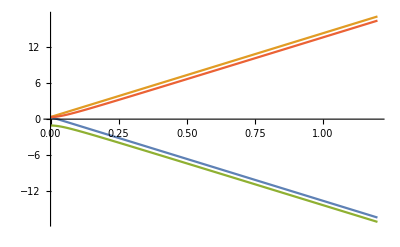

```mathematica
Plot[E1s,{b,0,1.2}]
```

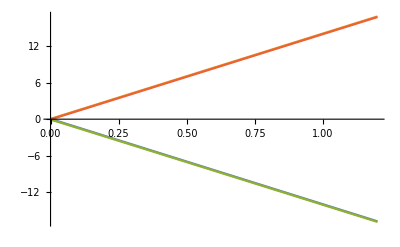

```mathematica
Plot[E2s,{b,0,1.2}]
```

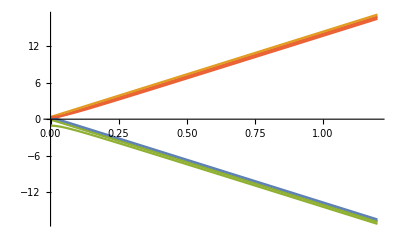

```mathematica
Show[%,%%]
```

The energy difference between the weak-field seeking states is quite insensitive to the magnetic field strength.

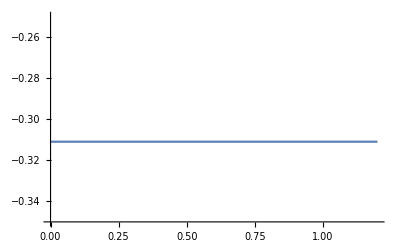

```mathematica
Plot[E2s⟦1⟧-E1s⟦1⟧,{b,0,1.2},PlotRange->{-0.35,-0.25}]
```

```mathematica
P5s=p/.NDSolve[{-1/2 p''[r]-1/r p[r]== -0.154 p[r],p[30]==1,p'[30]==-1},p,{r,30,1}]//First
```

InterpolatingFunction[{{1., 30.}}, <>]

```mathematica
P5s2=p/.NDSolve[{-1/2 p''[r]-(1+36 ⅇ^(-r/.45))/r p[r]== -0.154 p[r],p[30]==1,p'[30]==-1},p,{r,30,0}]//First
```

-14
InterpolatingFunction[{{5.72377 10   , 30.}}, <>]

```mathematica
nor=NIntegrate[{P5s[r]^2,P5s2[r]^2},{r,1,30}]
```

{1.15913×10^10,1.15305×10^10}

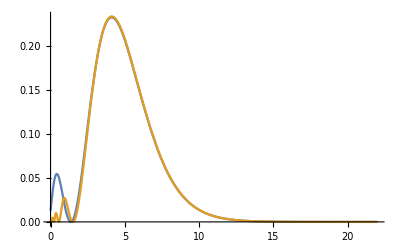

```mathematica
Plot[Evaluate@({P5s[r]^2,P5s2[r]^2}/nor),{r,0,22}]
```

```mathematica
nor
```

{1.15913×10^10,1.15305×10^10}

```mathematica
P5p=p/.NDSolve[{-1/2 p''[r]+(2/(2 r^2)-1/r)p[r]==-0.096  p[r],p[30]==1,p'[30]==-1},p,{r,30,1}]//First
```

InterpolatingFunction[{{1., 30.}}, <>]

```mathematica
P5p2=p/.NDSolve[{-1/2 p''[r]+(2/(2 r^2)-(1+36 ⅇ^(-r/.65))/r)p[r]==-0.096  p[r],p[30]==1,p'[30]==-1},p,{r,30,0.001}]//First
```

InterpolatingFunction[{{0.001, 30.}}, <>]

```mathematica
norp=NIntegrate[{P5p[r]^2,P5p2[r]^2},{r,2,30}]
```

{1.28912×10^7,1.27137×10^7}

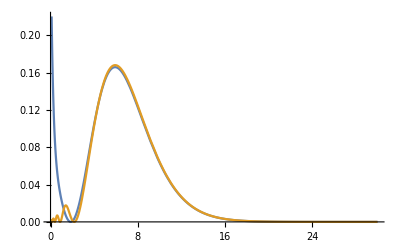

```mathematica
Plot[Evaluate@({P5p[r]^2,P5p2[r]^2}/norp),{r,.001,30}]
```

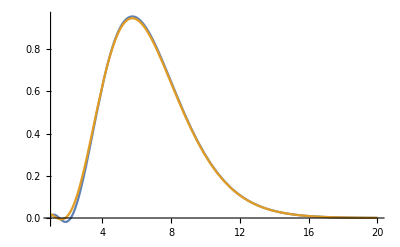

```mathematica
Plot[Evaluate@{r (P5p2[r]P5s2[r])/(√(nor⟦2⟧norp⟦2⟧)),r (P5p[r]P5s[r])/(√(nor⟦1⟧norp⟦1⟧))},{r,1,20}]
```

```mathematica
NIntegrate[{r (P5p2[r]P5s2[r])/(√(nor⟦2⟧norp⟦2⟧))},{r,0,20}]
```

{5.33856}